## Detailed Algebra for the Plasma Ramp Paper

```mathematica
ClearAll["Global`*"]
$Assumptions={Subscript[a, m0]∈Reals,Subscript[a, 0]∈Reals,Subscript[a, m0]<1,Subscript[β, m0]≥1,Subscript[β, 0]≥1};
```

#### Exact solution for the linear β_m ramp

The β function evolution equation is given by

```mathematica
1/2 β''[s]+(Subscript[k, β][s])^2 β[s]-1/β[s](1+(1/2 β'[s])^2)==0
```

β[s] k_β[s]^2-(1+1/4 β'[s]^2)/β[s]+β''[s]/2==0

The linear version can be derived by taking the derivative with respect to s

```mathematica
D[%,s]
```

k_β[s]^2 β'[s]+(β'[s] (1+1/4 β'[s]^2))/β[s]^2+2 β[s] k_β[s] k_β'[s]-(β'[s] β''[s])/(2 β[s])+1/2 β^(3)[s]==0

Using the first differential equation to simplify the second term

```mathematica
(Subscript[k, β][s])^2 β'[s]+β'[s]/β[s] (1/2 β''[s]+(Subscript[k, β][s])^2 β[s])+2 β[s] Subscript[k, β][s] Subscript[k, β]'[s]-(β'[s] β''[s])/(2 β[s])+1/2 Derivative[3][β][s]==0
```

k_β[s]^2 β'[s]+2 β[s] k_β[s] k_β'[s]+(β'[s] (β[s] k_β[s]^2+β''[s]/2))/β[s]-(β'[s] β''[s])/(2 β[s])+1/2 β^(3)[s]==0

At this point it is useful to define β_m in terms of k_β and introduce α_m

```mathematica
Subscript[k, β][s_]:=1/(Subscript[β, m][s]);
Subscript[β, m]'[s_]:=-2 Subscript[α, m][s];
Simplify[((Subscript[k, β][s])^2 β'[s]+2 β[s] Subscript[k, β][s] Subscript[k, β]'[s]+(β'[s] (β[s] (Subscript[k, β][s])^2+β''[s]/2))/β[s]-(β'[s] β''[s])/(2 β[s])+1/2 Derivative[3][β][s]) 2 (Subscript[β, m][s])^3]==0
```

8 β[s] α_m[s]+4 β_m[s] β'[s]+β_m[s]^3 β^(3)[s]==0

This equation can be solved for a linear β_m=β_m0-2 α_m0 s. Changing coordinates to β_m changes the derivatives to dβ/ds=-2 α_m dβ/dβ_mand (d^3 β)/ds^3=-8 α_m^3(d^3 β)/dβ_m^3 which simplifies the equation to

```mathematica
-β[Subscript[β, m]] Subscript[α, m0]+Subscript[α, m0] Subscript[β, m] β'[Subscript[β, m]]+Subscript[α, m0]^3 Subscript[β, m]^3 Derivative[3][β][Subscript[β, m]]==0;
```

It is a Cauchy Euler equation so we assume a solution of the form

```mathematica
β[x_]:=Subscript[c, n] x^n;
Simplify[(-β[Subscript[β, m]] Subscript[α, m0]+Subscript[α, m0] Subscript[β, m] β'[Subscript[β, m]]+Subscript[α, m0]^3 Subscript[β, m]^3 Derivative[3][β][Subscript[β, m]])/β[Subscript[β, m]]]==0
```

(-1+n) α_m0 (1+(-2+n) n α_m0^2)==0

and the solve the cubic equation for  the powers

```mathematica
Simplify[Solve[%,{n}]]
```

{{n→1},{n→1-(√(α_m0^2 (-1+α_m0^2)))/α_m0^2},{n→1+(√(α_m0^2 (-1+α_m0^2)))/α_m0^2}}

If α_m<1 then the square roots are imaginary we flip the sign inside the square root and write down the complete solution. Assuming the final solution is real places restraints on the constants and the final result is

```mathematica
Subscript[β, m][s_]:=Subscript[β, m0]-2 Subscript[α, m0] s;
Φ[s_]:=1/(2 Subscript[α, m0]) √(1-Subscript[α, m0]^2) Log[Subscript[β, m][s]]
β[s_]:=Subscript[β, m][s] (Subscript[c, 0]+Subscript[c, 1] Cos[2 Φ[s]]+Subscript[c, 2] Sin[2 Φ[s]]);
Simplify[8 β[s] Subscript[α, m0]+4 Subscript[β, m][s] β'[s]+(Subscript[β, m][s])^3 Derivative[3][β][s]]==0
```

True

The three constants can be reduced to 2 by plugging back into the original differential equation.

```mathematica
Simplify[Solve[1/2 β''[s]+β[s]/(Subscript[β, m][s])^2-1/β[s](1+(1/2 β'[s])^2)==0,Subscript[c, 0]]]
```

{{c_0→-(√(-1+c_1^2 (-1+α_m0^2)+c_2^2 (-1+α_m0^2)))/(√(-1+α_m0^2))},{c_0→(√(-1+c_1^2 (-1+α_m0^2)+c_2^2 (-1+α_m0^2)))/(√(-1+α_m0^2))}}

We keep only the positive term because c_0 must be positive for the β function to be positive.

```mathematica
Subscript[c, 0]=√(Subscript[c, 1]^2+Subscript[c, 2]^2+1/(1-Subscript[α, m0]^2));
Subscript[β, m0]=1;
Subscript[s, 0]=(Subscript[β, m0]-1)/(2 Subscript[α, m0]);
Simplify[Solve[{β[Subscript[s, 0]]==Subscript[β, 0],β'[Subscript[s, 0]]==-2 Subscript[α, 0]},{Subscript[c, 1],Subscript[c, 2]}]]
```

{{c_1→(1+α_0^2-2 α_0 α_m0 β_0+(-1+2 α_m0^2) β_0^2)/(2 (-1+α_m0^2) β_0),c_2→(α_0-α_m0 β_0)/(√(1-α_m0^2))}}

From which the results in the paper can be easily derived.

#### Higher order adiabatic solution

The first approach to come up with the higher order adiabatic solution is to use constants from the exact solution.

```mathematica
Subscript[c, 1]=1/2 (Subscript[β, 0]-(Subscript[γ, 0]-2 Subscript[α, 0] Subscript[α, m0]+Subscript[α, m0]^2 Subscript[β, 0])/(1-Subscript[α, m0]^2));
Subscript[c, 2]=(Subscript[α, 0]-Subscript[α, m0] Subscript[β, 0])/(√(1-Subscript[α, m0]^2));
Series[Subscript[c, 1],{Subscript[α, m0],0,2}]
Series[Subscript[c, 2],{Subscript[α, m0],0,2}]
```

1/2 (β_0-γ_0)+α_0 α_m0+(-β_0/2-γ_0/2) α_m0^2+O[α_m0]^3

α_0-β_0 α_m0+1/2 α_0 α_m0^2+O[α_m0]^3

Keeping only terms of order α_m0 we have two of the second order adiabatic constants. The third is from the square root

```mathematica
Subscript[c, 0]=√(Subscript[c, 1]^2+Subscript[c, 2]^2+1/(1-Subscript[α, m0]^2));
Series[Subscript[c, 0],{Subscript[α, m0],0,2}]
```

1/2 √(4+4 α_0^2+β_0^2-2 β_0 γ_0+γ_0^2)+((-α_0 β_0-α_0 γ_0) α_m0)/(√(4+4 α_0^2+β_0^2-2 β_0 γ_0+γ_0^2))+1/4 √(4+4 α_0^2+β_0^2-2 β_0 γ_0+γ_0^2) (-(4 (-α_0 β_0-α_0 γ_0)^2)/((4+4 α_0^2+β_0^2-2 β_0 γ_0+γ_0^2)^2)+(2 (2+4 α_0^2+β_0^2+γ_0^2))/(4+4 α_0^2+β_0^2-2 β_0 γ_0+γ_0^2)) α_m0^2+O[α_m0]^3

Working through the algebra the square root equals β_0+γ_0and the constant simplifies to

```mathematica
Subscript[c, 0]=1/2(Subscript[β, 0]+Subscript[γ, 0]-2 Subscript[α, 0] Subscript[α, m0])
```

#### Emittance growth due to adibaticity of the ramp

```mathematica
β0=βm (1-1/2 (1/(αm^2-1)+1));
FullSimplify[1/2(β0/βm+βm/β0)]
```

(8-12 αm^2+5 αm^4)/(8-12 αm^2+4 αm^4)

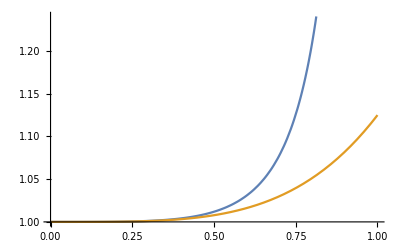

```mathematica
Plot[{(8-12 αm^2+5 αm^4)/(8-12 αm^2+4 αm^4),1+αm^4/8},{αm,0,1}]
```

```mathematica
Series[(8-12 αm^2+5 αm^4)/(8-12 αm^2+4 αm^4),{αm,0,4}]
```

1+αm^4/8+O[αm]^5